### Equilibrium Plot

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define the functions*)aeq[t_,κ_,λ_]:=-((1-Exp[-κ t/3]) (-Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1))

beq[t_,κ_,λ_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Use Manipulate to vary parameters κ and λ*)
(*Manipulate[
Plot[{aeq[t,κ,λ],beq[t,κ,λ]},{t,0,1},
PlotLegends->{"aeq(t; κ, λ)","beq(t; κ, λ)"},
PlotRange->All,AxesLabel->{"t","Value"},PlotLabel->"Plots of aeq(t; κ, λ) and beq(t; κ, λ)"],
{{κ,1},0.1,50},{{λ,1},0.01,20}]*)

Manipulate[Grid[{{Plot[aeq[t,κ,λ],{t,0,1},PlotLegends->{"aeq(t; κ, λ)"},PlotRange->All,AxesLabel->{"t","aeq(t; κ, λ)"},PlotLabel->"Plot of aeq(t; κ, λ)"],Plot[beq[t,κ,λ],{t,0,1},PlotLegends->{"beq(t; κ, λ)"},PlotRange->All,AxesLabel->{"t","beq(t; κ, λ)"},PlotLabel->"Plot of beq(t; κ, λ)"]}}],{{κ,1},0.1,50},{{λ,1},0.01,20}]
```

```mathematica
(*Compute the first and second derivatives of beq*)bPrime[t_,κ_,λ_]=D[beq[t,κ,λ],t]
bDoublePrime[t_,κ_,λ_]=D[beq[t,κ,λ],{t,2}]

(*Define the differential equation for a(t)*)
diffEq=a''[t]==-(λ/2) (bDoublePrime[t,κ,λ]+κ bPrime[t,κ,λ])

(*Solve the differential equation with boundary conditions*)
sol=DSolve[{diffEq,a[0]==0,a[1]==1},a[t],t]

(*Extract the solution for a(t)*)
aSol[t_]=a[t]/. sol[[1]]

(*Define the difference between a(t) and aeq(t)*)
diff[t_,κ_,λ_]:=aSol[t]-aeq[t,κ,λ]

(*Use Manipulate to set values of κ and λ*)Manipulate[Plot[{aSol[t],aeq[t,κ,λ],diff[t,κ,λ]},{t,0,1},PlotLegends->{"a(t)","aeq(t; κ, λ)","Difference (a(t) - aeq(t; κ, λ))"},PlotRange->All,AxesLabel->{"t","Value"},PlotLabel->"Comparison of a(t), aeq(t; κ, λ), and their Difference",PlotStyle->{Automatic,Automatic,{Dashed,Red}}],{{κ,1},0.1,2},{{λ,1},0.1,2}]
```

((1-ⅇ^(-(t κ)/3)) (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(2 (-1+ⅇ^κ) λ)+(ⅇ^(-(t κ)/3) κ (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(6 (-1+ⅇ^κ) λ)

(ⅇ^(-(t κ)/3) κ (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(3 (-1+ⅇ^κ) λ)+((1-ⅇ^(-(t κ)/3)) (1/9 ⅇ^((t κ)/3) κ^2 (-1+λ)+4/9 ⅇ^((2 t κ)/3) κ^2 (-1+λ)+ⅇ^(t κ) κ^2 (-1+λ)))/(2 (-1+ⅇ^κ) λ)-(ⅇ^(-(t κ)/3) κ^2 (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(18 (-1+ⅇ^κ) λ)

a''[t]==-1/2 λ ((ⅇ^(-(t κ)/3) κ (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(3 (-1+ⅇ^κ) λ)+((1-ⅇ^(-(t κ)/3)) (1/9 ⅇ^((t κ)/3) κ^2 (-1+λ)+4/9 ⅇ^((2 t κ)/3) κ^2 (-1+λ)+ⅇ^(t κ) κ^2 (-1+λ)))/(2 (-1+ⅇ^κ) λ)-(ⅇ^(-(t κ)/3) κ^2 (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(18 (-1+ⅇ^κ) λ)+κ (((1-ⅇ^(-(t κ)/3)) (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(2 (-1+ⅇ^κ) λ)+(ⅇ^(-(t κ)/3) κ (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(6 (-1+ⅇ^κ) λ)))

{{a[t]→(ⅇ^(-(t κ)/3) (-1+ⅇ^((t κ)/3)) (ⅇ^(κ/3)+ⅇ^(2 κ/3)+ⅇ^κ+ⅇ^((t κ)/3)+ⅇ^((2 t κ)/3)+ⅇ^(t κ)+ⅇ^(κ/3) λ+ⅇ^(2 κ/3) λ+ⅇ^κ λ-ⅇ^((t κ)/3) λ-ⅇ^((2 t κ)/3) λ-ⅇ^(t κ) λ))/(2 (-1+ⅇ^κ))}}

(ⅇ^(-(t κ)/3) (-1+ⅇ^((t κ)/3)) (ⅇ^(κ/3)+ⅇ^(2 κ/3)+ⅇ^κ+ⅇ^((t κ)/3)+ⅇ^((2 t κ)/3)+ⅇ^(t κ)+ⅇ^(κ/3) λ+ⅇ^(2 κ/3) λ+ⅇ^κ λ-ⅇ^((t κ)/3) λ-ⅇ^((2 t κ)/3) λ-ⅇ^(t κ) λ))/(2 (-1+ⅇ^κ))

```mathematica
N[diff[0.5, 5,20] ]
```

-6.59847+1/(-1.+2.71828^κ)0.5 2.71828^(-0.166667 κ) (-1.+2.71828^(0.166667 κ)) (0.+2.71828^(0.166667 κ)+2 2.71828^(0.333333 κ)+2.71828^(0.5 κ)+2.71828^(0.666667 κ)+2.71828^κ-1. 2.71828^(0.166667 κ) λ-1. 2.71828^(0.5 κ) λ+2.71828^(0.666667 κ) λ+2.71828^κ λ)

## Set values of lambda and kappa myself, and check that aeq(t) = a(t)

(2 ⅇ^(2-2 t) (1+ⅇ^2+ⅇ^4))/(-1+ⅇ^6)

-(4 ⅇ^(2-2 t) (1+ⅇ^2+ⅇ^4))/(-1+ⅇ^6)

a''[t]==-(4 ⅇ^(2-2 t) (1+ⅇ^2+ⅇ^4))/(-1+ⅇ^6)

{{a[t]→(ⅇ^(2-2 t) (-1+ⅇ^(2 t)))/(-1+ⅇ^2)}}

(ⅇ^(2-2 t) (-1+ⅇ^(2 t)))/(-1+ⅇ^2)

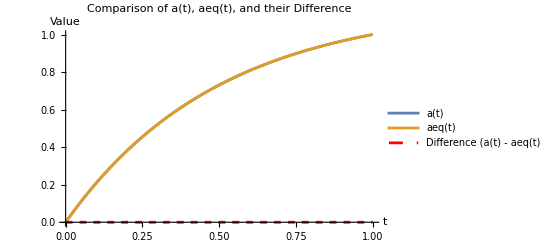

```mathematica
(*Set the parameters*)λ=1;
κ=6;

(*Define the function beq*)
beq[t_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Compute the first and second derivatives of beq*)
bPrime[t_]=D[beq[t],t]
bDoublePrime[t_]=D[beq[t],{t,2}]

(*Define the differential equation for a(t)*)
diffEq=a''[t]==-(λ/2) (bDoublePrime[t]+κ bPrime[t])

(*Solve the differential equation with boundary conditions*)
sol=DSolve[{diffEq,a[0]==0,a[1]==1},a[t],t]

(*Extract the solution for a(t)*)
aSol[t_]=a[t]/. sol[[1]]

(*Define the function aeq for comparison*)
aeq[t_]:=-((1-Exp[-κ t/3]) (-Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1))

(*Define the difference between a(t) and aeq(t)*)
diff[t_]:=aSol[t]-aeq[t]

(*Plot a(t),aeq(t),and their difference*)
Plot[{aSol[t],aeq[t],diff[t]},{t,0,1},PlotLegends->{"a(t)","aeq(t)","Difference (a(t) - aeq(t))"},PlotRange->All,AxesLabel->{"t","Value"},PlotLabel->"Comparison of a(t), aeq(t), and their Difference",PlotStyle->{Automatic,Automatic,{Dashed,Red}}]
```

### Checking that beq() is the best response to aeq()

(2 ⅇ^(2-2 t) (1+ⅇ^2+ⅇ^4))/(-1+ⅇ^6)

-(4 ⅇ^(2-2 t) (1+ⅇ^2+ⅇ^4))/(-1+ⅇ^6)

b''[t]==-(4 ⅇ^(2-2 t) (1+ⅇ^2+ⅇ^4))/(-1+ⅇ^6)

{{b[t]→(ⅇ^(2-2 t) (-1+ⅇ^(2 t)))/(-1+ⅇ^2)}}

(ⅇ^(2-2 t) (-1+ⅇ^(2 t)))/(-1+ⅇ^2)

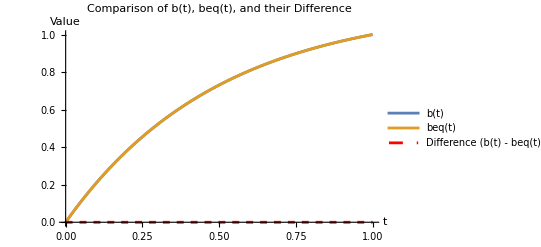

```mathematica
(*Set the parameters*)λ=1;
κ=6;

(*Define the function aeq*)
aeq[t_]:=-((1-Exp[-κ t/3]) (-Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1))

(*Compute the first and second derivatives of aeq*)
aPrime[t_]=D[aeq[t],t]
aDoublePrime[t_]=D[aeq[t],{t,2}]

(*Define the differential equation for b(t)*)
diffEqB=b''[t]==-1/(2 λ) (aDoublePrime[t]+κ aPrime[t])

(*Solve the differential equation with boundary conditions*)
solB=DSolve[{diffEqB,b[0]==0,b[1]==1},b[t],t]

(*Extract the solution for b(t)*)
bSol[t_]=b[t]/. solB[[1]]

(*Define the function beq for comparison*)
beq[t_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Define the difference between b(t) and beq(t)*)
diffB[t_]:=bSol[t]-beq[t]

(*Plot b(t),beq(t),and their difference*)
Plot[{bSol[t],beq[t],diffB[t]},{t,0,1},PlotLegends->{"b(t)","beq(t)","Difference (b(t) - beq(t))"},PlotRange->All,AxesLabel->{"t","Value"},PlotLabel->"Comparison of b(t), beq(t), and their Difference",PlotStyle->{Automatic,Automatic,{Dashed,Red}}]
```

#### Calculate derivatives of aeq(t) and beq(t)

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define the function aeq*)aeq[t_]:=-((1-Exp[-κ t/3]) (-Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1))

(*Calculate the derivative with respect to t*)
aeqPrime=D[aeq[t],t];

(*Simplify the derivative*)
simplifiedAeqPrime=Simplify[aeqPrime];

(*Output the simplified derivative*)
simplifiedAeqPrime
```

(ⅇ^(-(t κ)/3) κ (-3 ⅇ^((4 t κ)/3) (-1+λ)+ⅇ^(κ/3) (1+λ)+ⅇ^(2 κ/3) (1+λ)+ⅇ^κ (1+λ)))/(6 (-1+ⅇ^κ))

```mathematica
(*Define the function beq*)beq[t_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Calculate the derivative with respect to t*)
beqPrime=D[beq[t],t];

(*Simplify the derivative*)
simplifiedBeqPrime=Simplify[beqPrime];

(*Output the simplified derivative*)
simplifiedBeqPrime
```

(ⅇ^(-(t κ)/3) κ (3 ⅇ^((4 t κ)/3) (-1+λ)+ⅇ^(κ/3) (1+λ)+ⅇ^(2 κ/3) (1+λ)+ⅇ^κ (1+λ)))/(6 (-1+ⅇ^κ) λ)

```mathematica
ClearAll["Global`*"]
(*Define the function aeq*)aeq[t_,κ_,λ_]:=-((1-Exp[-κ t/3]) (-Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1))

(*Define the function beq*)
beq[t_,κ_,λ_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Calculate the derivatives with respect to t*)
aeqPrime[t_,κ_,λ_]=D[aeq[t,κ,λ],t]
beqPrime[t_,κ_,λ_]=D[beq[t,κ,λ],t]

(*Simplify the derivatives*)
simplifiedAeqPrime[t_,κ_,λ_]:=Simplify[aeqPrime[t,κ,λ]]
simplifiedBeqPrime[t_,κ_,λ_]:=Simplify[beqPrime[t,κ,λ]]

(*Use Manipulate to set values of κ and λ and plot the functions*)
Manipulate[Column[{Plot[{aeq[t,κ,λ],beq[t,κ,λ]},{t,0,1},PlotLegends->{"aeq(t)","beq(t)"},PlotRange->All,AxesLabel->{"t","Value"},PlotLabel->"Plots of aeq(t) and beq(t)"],Plot[{simplifiedAeqPrime[t,κ,λ],simplifiedBeqPrime[t,κ,λ]},{t,0,1},PlotLegends->{"simplifiedAeqPrime","simplifiedBeqPrime"},PlotRange->All,AxesLabel->{"t","Value"},PlotLabel->"Plots of simplifiedAeqPrime and simplifiedBeqPrime"]}],{{κ,1},0.1,10},{{λ,1},0.1,10}]
```

-((1-ⅇ^(-(t κ)/3)) (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(2 (-1+ⅇ^κ))-(ⅇ^(-(t κ)/3) κ (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)-ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(6 (-1+ⅇ^κ))

((1-ⅇ^(-(t κ)/3)) (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(2 (-1+ⅇ^κ) λ)+(ⅇ^(-(t κ)/3) κ (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(6 (-1+ⅇ^κ) λ)

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

```mathematica
((1-ⅇ^(-(t κ)/3)) (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(2 (-1+ⅇ^κ) λ)+(ⅇ^(-(t κ)/3) κ (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(6 (-1+ⅇ^κ) λ)
```

((1-ⅇ^(-(t κ)/3)) (1/3 ⅇ^((t κ)/3) κ (-1+λ)+2/3 ⅇ^((2 t κ)/3) κ (-1+λ)+ⅇ^(t κ) κ (-1+λ)))/(2 (-1+ⅇ^κ) λ)+(ⅇ^(-(t κ)/3) κ (ⅇ^((t κ)/3) (-1+λ)+ⅇ^((2 t κ)/3) (-1+λ)+ⅇ^(t κ) (-1+λ)+ⅇ^(κ/3) (1+ⅇ^(κ/3)+ⅇ^(2 κ/3)) (1+λ)))/(6 (-1+ⅇ^κ) λ)

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 0.0000204286 is not a valid variable.

D::ivar: 0.0204286 is not a valid variable.

D::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

```mathematica
ClearAll["Global`*"]
(*Initialize the parameters*)
tValue=0.2;
λValue=5;
κValue=1;

(*Define the function aeq*)
aeq[t_,κ_,λ_]:=-((1-Exp[-κ t/3]) (-Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1))

(*Define the function beq*)
beq[t_,κ_,λ_]:=((1-Exp[-κ t/3]) (Exp[κ/3] (Exp[κ/3]+Exp[2 κ/3]+1) (λ+1)+(λ-1) Exp[κ t/3]+(λ-1) Exp[2 κ t/3]+(λ-1) Exp[κ t]))/(2 (Exp[κ]-1) λ)

(*Calculate the derivatives with respect to t*)
aeqPrime[t_,κ_,λ_]:=D[aeq[t,κ,λ],t]
beqPrime[t_,κ_,λ_]:=D[beq[t,κ,λ],t]

(*Simplify the derivatives symbolically*)
simplifiedAeqPrime[t_,κ_,λ_]:=Simplify[aeqPrime[t,κ,λ]]
simplifiedBeqPrime[t_,κ_,λ_]:=Simplify[beqPrime[t,κ,λ]]

(*Calculate the values using the initialized parameters*)
aeqValue=aeq[tValue,κValue,λValue]
beqValue=beq[tValue,κValue,λValue]
simplifiedAeqPrimeValue=simplifiedAeqPrime[t,κ,λ]/. {t->tValue,κ->κValue,λ->λValue}
simplifiedBeqPrimeValue=simplifiedBeqPrime[t,κ,λ]/. {t->tValue,κ->κValue,λ->λValue}

(*Print the values*)
N[{aeqValue,beqValue,simplifiedAeqPrimeValue,simplifiedBeqPrimeValue}]
```

0.424839

0.188049

1.87856

0.944374

{0.424839,0.188049,1.87856,0.944374}